# Quasireversible cyclic voltammetry with coupled homogeneous reactions

This notebook shows how a cyclic voltammogram for the square scheme

O+e | ⇌ | R
k_-1 ⥮ k_(+1) |   | k_-2 ⥮ k_(+2)
A+e | ⇌ | B

can be simulated using implicit finite difference methods. In this implementation the cross reaction is included but a linear approximation is used.

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
Needs["Notation`"](*allows the creation of new symbols*);
```

```mathematica
Symbolize[Subscript[k, _]];
Symbolize[Subscript[K, _]];
Symbolize[Subscript[ΔE, _]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionB={
PlotStyle->{Red,AbsoluteThickness[0.5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["√πχ",FontFamily->  "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

The show status function was written by Theodore Gray and published in The Mathematica Journal Vol. 7-3. It is useful for following the progress of longer calculations.

```mathematica
ShowStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]]
```

## Make diagonals

```mathematica
Clear[makeSquareDiagonals];

makeSquareDiagonals[m_Integer,d_,a_][khf1_,khb1_,khf2_,khb2_]:=Module[{x,yConst,z},
x=Table[-a*d*a^(3-2*j)*IdentityMatrix[4],{j,2,m-1}];
z=Table[-d*a^(3-2*j)*IdentityMatrix[4],{j,2,m-2}];
yConst=Table[(1+(1+a)*d*a^(3-2*j))*IdentityMatrix[4]+{{khf1,0,-khb1,0},{0,khf2,0,-khb2},{-khf1,0,+khb1,0},{0,-khf2,0,khb2}},{j,2,m-1}];
{x,yConst,z}]
```

## Set Up Solution

```mathematica
Clear[tridiagMatSolver];

tridiagMatSolver=Compile[{{x,_Real,3},{y,_Real,3},{z,_Real,3},{b,_Real,2}},Module[{len=Length[b],sol=Table[Table[0.,{Length[b⟦1⟧]}],{Length[b]}],aux,β=Table[Table[0.,{Length[x⟦1⟧]},{Length[x⟦1⟧]}],{Length[b]}],iter=0},

aux=Inverse[y⟦1⟧];
sol⟦1⟧=aux.b⟦1⟧;
Do[β⟦iter⟧=aux.z⟦iter-1⟧;
aux=Inverse[(y⟦iter⟧-x⟦iter⟧.β⟦iter⟧)];
sol⟦iter⟧=aux.(b⟦iter⟧-x⟦iter⟧.sol⟦iter-1⟧),{iter,2,len}]; 			Do[sol⟦iter⟧-=β⟦iter+1⟧.sol⟦iter+1⟧,{iter,len-1,1,-1}];
sol]];
```

```mathematica
Clear[yVar,vect];

yVar:={{kcf*#⟦4⟧,-kcb*#⟦3⟧,-kcb*#⟦2⟧,kcf*#⟦1⟧},{-kcf*#⟦4⟧,kcb*#⟦3⟧,kcb*#⟦2⟧,-kcf*#⟦1⟧},{-kcf*#⟦4⟧,kcb*#⟦3⟧,kcb*#⟦2⟧,-kcf*#⟦1⟧},{kcf*#⟦4⟧,-kcb*#⟦3⟧,-kcb*#⟦2⟧,kcf*#⟦1⟧}}&;


vect:={#⟦1⟧+kcf*#⟦1⟧*#⟦4⟧-kcb*#⟦3⟧*#⟦2⟧,#⟦2⟧-kcf*#⟦1⟧*#⟦4⟧+kcb*#⟦3⟧*#⟦2⟧,#⟦3⟧-kcf*#⟦1⟧*#⟦4⟧+kcb*#⟦3⟧*#⟦2⟧,#⟦4⟧+kcf*#⟦1⟧*#⟦4⟧-kcb*#⟦3⟧*#⟦2⟧}&
```

```mathematica
Clear[implicitSolveSquareExp];

implicitSolveSquareExp[m_Integer,n_Integer,d_,a_,{lowerLimit_,upperLimit_},{ksStar1_,ksStar2_,khf1_,khb1_,khf2_,khb2_,ΔEor_,ΔEab_,cOi_,cAi_,α_}]:=Module[{range,τ,y1,x1,z1,x,y,yConst,z,initial,b2,b3,solveNext},

range =2*(Abs[upperLimit]+Abs[lowerLimit]);
τ=range/(n-1);
b2={{(1.+a)^2,0,0,0},{0,0,(1.+a)^2,0},{(1.+a)^2,(1.+a)^2,0,0},{0,0,(1.+a)^2,(1.+a)^2}};
b3={{1,0,0,0},{0,0,1,0},{1,1,0,0},{0,0,1,1}};
initial=Table[{cOi,0,cAi,0},{m}];

{x,yConst,z}=makeSquareDiagonals[m,d,a][khf1,khb1,khf2,khb2];
x1=x⟦1⟧;
y1=yConst⟦1⟧;
z1=z⟦1⟧;

solveNext[list_,k_]:=Module[{ξ1,ξ2,b1,b,tmp},
ShowStatus[k];

ξ1=If[k>(n+1)/2,Exp[upperLimit-ΔEor-range+(τ*(k-1))],Exp[upperLimit-ΔEor-(τ*(k-1))]];

ξ2=If[k>(n+1)/2,Exp[upperLimit-ΔEab-range+(τ*(k-1))],Exp[upperLimit-ΔEab-(τ*(k-1))]];

b=list[[2;;-2]];
y=yConst+yVar/@b;
b=vect/@b;
b⟦-1⟧+={cOi*d*a^(5-2*m),0.,cAi*d*a^(5-2*m),0.};

b1=Inverse[{{a*(2+a)+a*(1+a)*ksStar1*ξ1^-α,-a*(1+a)*ksStar1*ξ1^(1.-α),0,0},{0,0,a*(2+a)+a*(1+a)*ksStar2*ξ2^-α,-a*(1+a)*ksStar2*ξ2^(1.-α)},{a*(2+a),a*(2+a),0,0},{0,0,a*(2+a),a*(2+a)}}];

y⟦1⟧+=(x1.b1.b2);
z⟦1⟧=z1-(x1.b1.b3);

tmp=tridiagMatSolver[x,y,z,b];

Join[{b1.b2.tmp⟦1⟧-b1.b3.tmp⟦2⟧},tmp,{{cOi,0.,cAi,0.}}]
];
FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Set Constants & variables

```mathematica
Clear[𝔽,ℝ,𝕋,𝒻];

𝔽=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)

ℝ=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)

𝕋=298.;(*temperature*)

𝒻=𝔽/(ℝ*𝕋);
```

### Set electrochemical variables

```mathematica
Clear[α,𝒟,upperLimit,lowerLimit,𝕥,ksDim1,ksDim2,Subscript[ΔE, OR],Subscript[ΔE, AB],Subscript[K, OA],Subscript[K, RB],Kc];

α=0.5;(*transfer coefficient, generally taken as being 0.5*)

𝒟=1.*^-5;(*diffusion coefficient*)

upperLimit=30.(*initial potential versus the formal potential*);

lowerLimit=-10.(*switching potential versus the formal potential*);

𝕥 =2*(Abs[upperLimit]+Abs[lowerLimit]);(*the region or range of the sweep*)

ksDim1=1.*^4;(*dimensionless rate constant*)

ksDim2=1.*^4;(*dimensionless rate constant*)

Subscript[ΔE, OR]=𝒻*0;

Subscript[ΔE, AB]=𝒻*0.5;

Subscript[K, RB]=1.*^4;

Subscript[K, OA]=Subscript[K, RB]*Exp[Subscript[ΔE, OR]-Subscript[ΔE, AB]];

Kc=Subscript[K, OA]/Subscript[K, RB];
```

### Set simulation variables

```mathematica
Clear[n,τ,khf1,khf2,khb1,khb2,kcb,kcf,𝔻,a,m,ksStar1,ksStar2,b2,b3,conc,c]

n=Round[𝕥/(0.01*𝒻)](*2 mV steps*);

τ=𝕥/(n-1)(*calculation of the incremental time/potential step*);

khb1=τ*1.*^0;

khf1=khb1*Subscript[K, OA];

khf2=τ*1.*^4;

khb2=khf2/Subscript[K, RB];

kcb=1.*^2;

kcf=kcb*Kc;

𝔻=5.Max[khf1,khb1,khf2,khb2,kcb,kcf,0.4];

a=1.1;
temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=mm/.temp⟦1⟧//Ceiling;(*number of spacial grid points*)


Clear[temp];

ksStar1=ksDim1*Sqrt[(2*𝕥)/(𝔻*(1+a)*(n-1))];

ksStar2=ksDim2*Sqrt[(2*𝕥)/(𝔻*(1+a)*(n-1))];

cOi=1/(1+Subscript[K, OA]);

cAi=Subscript[K, OA]/(1+Subscript[K, OA]);
```

```mathematica
{upperLimit,lowerLimit,𝕥,ksDim1,ksDim2,Subscript[ΔE, OR],Subscript[ΔE, AB],Subscript[K, OA],Subscript[K, RB],n,τ,khf1,khf2,khb1,khb2,kcb,kcf,𝔻,a,m,ksStar1,ksStar2}
```

{30.,-10.,80.,10000.,10000.,0.,19.4707,0.0000349942,10000.,205,0.392157,0.0000137232,3921.57,0.392157,0.392157,100.,3.49942×10^-7,19607.8,1.1,76,43.6436,43.6436}

## Solve it

```mathematica
c=implicitSolveSquareExp[m,n,𝔻,a,{lowerLimit,upperLimit},{ksStar1,ksStar2,khf1,khb1,khf2,khb2,Subscript[ΔE, OR],Subscript[ΔE, AB],cOi,cAi,α}];//Timing
```

{0.920494,Null}

Check mass balance

```mathematica
m
Map[Total[#,2]&,c]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Plot CV

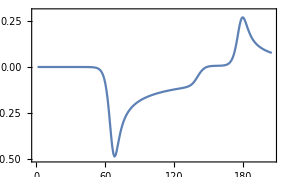

```mathematica
cv1=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c⟦All,All,1⟧];

cv2=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c⟦All,All,3⟧];

cv3=cv1+cv2;

plot1=ListPlot[cv3,PlotRange-> {-.5,.3}]
```

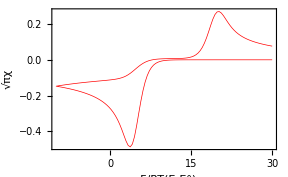

```mathematica
cv4=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-τ(j-1)],cv3⟦j⟧},{j,1,Length[cv3]}];

ListPlot[cv4,optionB,PlotRange->All]
```